NC::Directory: You are using a paclet version of NCAlgebra.

NCAlgebra::SmallCapSymbolsNonCommutative: All lower cap single letter symbols (e.g. a,b,c,...) were set as noncommutative.

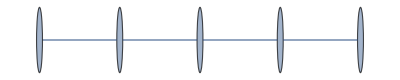
G: -Graphics-

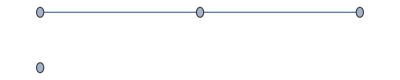
H: -Graphics-

41

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Monomial order:

> t_(1,1)<t_(1,2)<t_(1,3)<t_(1,4)<t_(2,1)<t_(2,2)<t_(2,3)<t_(2,4)<t_(3,1)<t_(3,2)<t_(3,3)<t_(3,4)<t_(4,1)<t_(4,2)<t_(4,3)<t_(4,4)<t_(5,1)<t_(5,2)<t_(5,3)<t_(5,4)

* Reduce and normalize initial set

> Initial set could not be reduced

* Computing initial set of obstructions

> MAJOR Iteration 1, 67 polys in the basis, 175 obstructions

> MAJOR Iteration 2, 116 polys in the basis, 506 obstructions

$Aborted

```mathematica
<< NC`
<< NCAlgebra`
<< NCGBX`

(* We are investigating the graph homomorphism game G -> K_k, i.e., the graph coloring game *)

kColorableGraph[k_, n_] := Module[ 
{vertices, colors, edges = {}, indices, partition, splitPoints, subset, Ni, Nj, graph},
vertices = Range[n]; (* list of n vertices *)
colors = Table[{}, {k}]; (* table of the colors *)

indices = RandomSample[Range[n]];
partition = {}; (* Split into k clusters of colors *)
splitPoints = RandomSample[Range[1, n - 1], k - 1];
splitPoints = Sort[splitPoints];

For [i = 1, i <= k - 1, i++,
If[i == 1,
subset = indices[[Range[splitPoints[[1]]]]];
AppendTo[partition, subset]
];

If [i != 1,
subset = indices[[Range[splitPoints[[i-1]]+ 1, splitPoints[[i]]]]];
AppendTo[partition, subset]
];

If [ i ==  k - 1,
subset = indices[[Range[splitPoints[[k-1]] + 1, n]]];
AppendTo[partition, subset]
];
];

For[i = 1, i <= k, i++,
For[j = i + 1, j <= k, j++,
Ni = Length[partition[[i]]];
Nj = Length[partition[[j]]];
For[p = 1, p <= Ni, p++,
For[q = 1, q <= Nj, q++,
AppendTo[edges, UndirectedEdge[partition[[i, p]], partition[[j, q]]]];
]
]
]
];

graph=Graph[vertices,edges,VertexLabels->"Name"];
	
graph
];


(* G is given as a c-colorable graph *)
GraphColoringQC[G_] := Module[{Inc, e, V, E, c, rels = {}, convertedList},
Inc = IncidenceMatrix[G];
V = Dimensions[Inc][[1]];
E = Dimensions[Inc][[2]];
c = VertexChromaticNumber[G];

(* Projection generators of the unital *-algebras *)
e = Table[Subscript[x, v, i], {v, 1, V}, {i, 1, c}];
SetNonCommutative[x];
convertedList={};
For[v = 1, v <= V, v++,
For[i = 1, i <= c, i++,
AppendTo[convertedList, e[[v, i]]]
]
];
SetMonomialOrder[convertedList];


For[v = 1, v <= V, v++,
For[i = 1, i <= c, i++,
For[j = i + 1, j <= c, j++,
AppendTo[rels, e[[v, i]] ** e[[v, j]]];
];
AppendTo[rels, aj[e[[v, i]]] - e[[v, i]]];
AppendTo[rels, e[[v, i]] ** e[[v, i]] - e[[v, i]]];
];
AppendTo[rels, Sum[e[[v, i]], {i, 1, c}] - 1];
];

For [u = 1, u <= V, u++,
For[v = u  + 1, v <= V, v++,
(* Search for their common edge *)
For [d = 1, d <= E, d++,
If[Inc[[u, d]] == 1 && Inc[[v, d]] == 1,
For[i = 1, i <= c, i++,
AppendTo[rels, e[[u, i]] ** e[[v, i]]];
];
Break[];
]
]
]
];

gb = NCMakeGB[rels, 10];


Print[gb];
Print[Length[rels]];
Print["Basis dimension: ", Length[gb]];
] ;


GraphHomomorphismQC[G_, H_] := Module[{IncG, IncH, VG, EG, VH, EH, e, convertedList, rels = {}, AdjG, AdjH},
IncG = IncidenceMatrix[G];
IncH = IncidenceMatrix[H];
VG = Dimensions[IncG][[1]];
EG = Dimensions[IncG][[2]];
VH = Dimensions[IncH][[1]];
EH = Dimensions[IncH][[2]];

e = Table[Subscript[t, v, y], {v, 1, VG}, {y, 1, VH}];
SetNonCommutative[t];
convertedList={};
For[v = 1, v <= VG, v++,
For[y= 1, y <= VH, y++,
AppendTo[convertedList, e[[v, y]]]
]
];
SetMonomialOrder[convertedList];

For[v = 1, v <= VG, v++,
AppendTo[rels, Sum[e[[v, y]], {y, 1, VH}] - 1];
For[y = 1, y <= VH, y++,
AppendTo[rels, e[[v, y]] ** e[[v, y]] - e[[v, y]]];
]
];

AdjG = AdjacencyMatrix[G];
AdjH = AdjacencyMatrix[H];

For[v = 1, v <= VG, v++,
For [w = v + 1, w <= VG, w++,
If[AdjG[[v, w]] == 1,
For [x = 1, x <= VH, x++,
For[y = x + 1, y <= VH, y++,
If[AdjH[[x, y]] != 1,
AppendTo[rels, e[[v, x]] ** e[[w, y]]];
]
]
]
]
]
];
Print[Length[rels]];
gb = NCMakeGB[rels, 10];

Print[gb];
];

g1=Graph[{1, 2, 3, 4, 5}, {1<-> 2, 2<-> 3, 3<->4, 4<->5}];
(*g2=CompleteGraph[5];*)
g2 = Graph[{1, 2, 3, 4}, {1<-> 2, 2<-> 3}];

Print["G: ", g1];
Print["H: ", g2];

GraphHomomorphismQC[g1, g2];


(* Use SDP to verify the  *)

(*g = kColorableGraph[3, 10];

GraphColoringQC[g];*)
```

(1 | 0
1 | 1
0 | 1
0 | 0
0 | 0)SparseArray[…]

{1.73205,1.,0.}{2.,1.,1.}

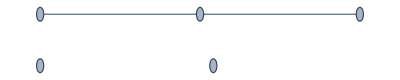

G: -Graphics-  H: -Graphics-

0.911231

```mathematica
g1=Graph[{1, 2, 3, 4, 5}, {1<-> 2, 2<-> 3}];
g2=CompleteGraph[3];

GraphSimilarity[g1_, g2_] := Module[ {Inc1, Inc2, sigmaVec1, sigmaVec2, len, cosSim},
Inc1 = IncidenceMatrix[g1];
Inc2 = IncidenceMatrix[g2];
Print[MatrixForm[Inc1], Inc2];

(*If[Dimensions[Inc1][[1]] != Dimensions[Inc2][[1]],
Return[" Exception: Unequal Vertex Number "]
];*)

sigmaVec1 = SingularValueList[Inc1];
sigmaVec2 = SingularValueList[Inc2];

len = Max[Length[sigmaVec1], Length[sigmaVec2]];
sigmaVec1 = PadRight[sigmaVec1, len];
sigmaVec2 = PadRight[sigmaVec2, len];
Print[N[sigmaVec1], N[sigmaVec2]];

cosSim = Dot[sigmaVec1, sigmaVec2] / (Norm[sigmaVec1] Norm[sigmaVec2]);

Print["G: ", g1, "  H: ", g2];
N[cosSim]
]

(*计算编辑距离*)
GraphSimilarity[g1, g2]
```